# Mixed Strategy on an interval

## Section 1. mixing continuously on interval m1,m2 with distribution function distCDF[e].

```mathematica
(*Basics*)
m1:=b-a;  (*Lower bound of the mixing dist*)
m2:=Sqrt[V]-(b-a); (*Upper bound of the mixing dist*)
(*Set values for plotting*)
V:=100;
a:=-2; 
b:=2;
```

```mathematica
(*Define 3 possible distributions for distCDF[e]:uniform,increasing,decreasing to see which one is better able to force profits to be flat on the interval*)
uniformIntervalCDF[e_]:=Piecewise[{{(e-m1)/(m2-m1),m1<e<m2},{1, e>=m2},{0,x<=m1}}];
uniformIntervalPDF[e_]:= uniformIntervalCDF'[e];
increasingIntervalCDF[e_]:=Piecewise[{{((e-m1)/(m2-m1))^2,m1<e<m2},{1, e>=m2},{0,x<=m1}}];
increasingIntervalPDF[e_]:=increasingIntervalCDF'[e];
decreasingIntervalCDF[e_]:=Piecewise[{{((m1-e)(m1-2m2+e))/(m2-m1)^2,m1<e<m2},{1, e>=m2},{0,x<=m1}}];
decreasingIntervalPDF[e_]:=decreasingIntervalCDF'[e];
```

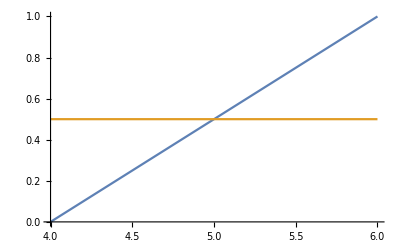
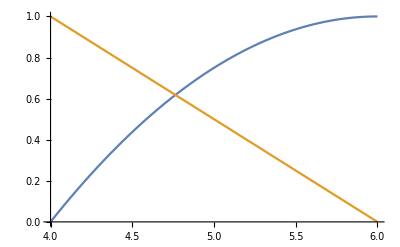
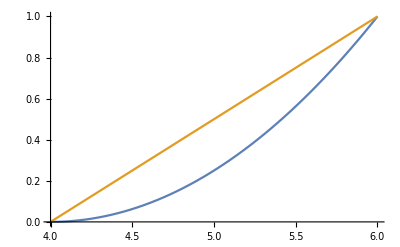
{-Graphics-,-Graphics-,-Graphics-,4,6}

```mathematica
(*Plotting the mixing distributions*)
p1=Plot[{uniformIntervalCDF[e],uniformIntervalPDF[e]},{e,m1,m2}];
p2=Plot[{decreasingIntervalCDF[e],decreasingIntervalPDF[e]},{e,m1,m2}];
p3=Plot[{increasingIntervalCDF[e],increasingIntervalPDF[e]},{e,m1,m2}];
{p1,p2,p3,m1,m2}
```